This notebook includes an example from Mathematica, StackExchange at https://mathematica.stackexchange.com/questions/79582/cross-correlation-with-timeseries

```mathematica
{pepsi,mcds}=TimeSeries[FinancialData[{"NYSE",#},"Price",{DateObject[{2012,12,31}],DateObject[{2015,3,31}],"Week"}]]&/@{"PEP","MCD"}
```

{TimeSeries[…],TimeSeries[…]}

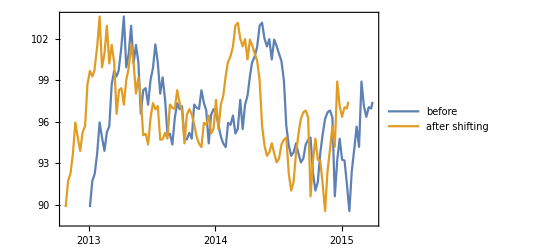

```mathematica
DateListPlot[{mcds,TimeSeriesShift[mcds,Quantity[-10,"Week"]]},PlotLegends->{"before","after shifting"}]
```

```mathematica
crossCorrelation[tsX_,tsY_,shift_?QuantityQ]:=Module[{μX=Mean@tsX,σX=StandardDeviation@tsX,μY=Mean@tsY,σY=StandardDeviation@tsY,tsYShift,xValues,yValues,minLength,pairs},tsYShift=TimeSeriesShift[tsY,shift];
xValues=Select[tsX["Path"],#[[1]]≤tsYShift["LastTime"]&][[All,2]];
yValues=Select[tsYShift["Path"],#[[1]]≥tsX["FirstTime"]&][[All,2]];
minLength=Min[Length/@{xValues,yValues}];
pairs=Transpose[{xValues[[;;minLength]],yValues[[;;minLength]]}];
Last[FoldList[Function[{running,next},running+(next[[1]]-μX) (next[[2]]-μY)],0,pairs]]/(minLength σX σY)]
```

```mathematica
crossCorrelation[pepsi,mcds,Quantity[-10,"Weeks"]]
```

-0.578546

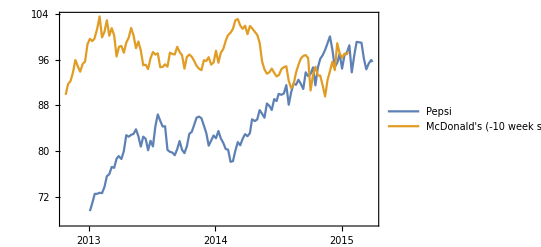

```mathematica
DateListPlot[{pepsi,TimeSeriesShift[mcds,Quantity[-10,"Week"]]},PlotLegends->{"Pepsi","McDonald's (-10 week shift)"}]
```

```mathematica
Round[Correlation[FinancialData["NYSE:DO","CumulativeReturn",{DateObject[{2012,12,31}],DateObject[{2015,3,31}],"Day"},"Value"],FinancialData["NYSE:RIG","CumulativeReturn",{DateObject[{2012,12,31}],DateObject[{2015,3,31}],"Day"},"Value"]],0.01]
```

0.91